```mathematica
eqn={phi'[t]==z[t] , z'[t]==-3*z[t]*H[t]-1*phi[t]+1*phi[t]^3,H'[t]==-3*H[t]^2+1*phi[t]^3/2-1*phi[t]^4/4+0.1, phi[0]==0.00001 , z[0]==0.0001,H[0]==1/3*Sqrt[z[0]^2/2+phi[0]^2/2-phi[0]^4/4+0.1]};
```

```mathematica
sol=NDSolve[eqn,{phi[t],z[t], H[t]},{t,-10,15}]
```

{{phi[t]→InterpolatingFunction[{{-10., 15.}}, <>][t],z[t]→InterpolatingFunction[{{-10., 15.}}, <>][t],H[t]→InterpolatingFunction[{{-10., 15.}}, <>][t]}}

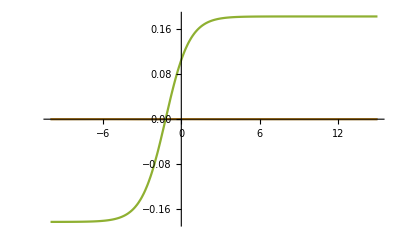

```mathematica
Plot[{phi[t]/.sol,z[t]/.sol, H[t]/.sol},{t,-10,15}]
```

```mathematica
Quit[]
```